## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGMi";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_PGMi_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((2pg)^c⇌(3pg)^c)^PGMi

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 2.9815 | 2.83242
3.13057 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.00021 | 0.0002
0.00022 |  |  | 7 | 30 |  | 
1 | 2pg | 0.000097 | 0.000092
0.000102 |  |  | 7 | 30 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 41.7812 | 37.9829
45.5795 |  | 7 | 37 |  | 
1 | 2pg | Null | 18.9914 | 15.1932
22.7897 |  | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
(*kcatPriorities = {1,1};*)
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌(3pg)^c)^PGMi

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 2.9815 | 2.83242
3.13057 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.00021 | 0.0002
0.00022 |  |  | 7 | 30 |  | 
1 | 2pg | 0.000097 | 0.000092
0.000102 |  |  | 7 | 30 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 41.7812 | 37.9829
45.5795 |  | 7 | 37 |  | 
1 | 2pg | Null | 18.9914 | 15.1932
22.7897 |  | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMi[c] + 2pg[c] <=> E_PGMi[c]&2pg",

				"E_PGMi[c]&2pg <=> E_PGMi[c]&3pg",
				
				"E_PGMi[c]&3pg <=> E_PGMi[c] + 3pg[c]"}; (*Reaction now properly flipped*)


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGMi^c)_^+(2pg)^c⇌(PGMi^c&(2pg)^c)_^)^PGMi1,((PGMi^c&(3pg)^c)_^⇌(PGMi^c)_^+(3pg)^c)^PGMi2,((PGMi^c&(2pg)^c)_^⇌(PGMi^c&(3pg)^c)_^)^PGMi3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMi^c)_^+(2pg)^c⇌(PGMi^c&(2pg)^c)_^)^PGMi1,Overscript[(PGMi^c&(3pg)^c)_^⇌(PGMi^c)_^+(3pg)^c, PGMi2],((PGMi^c&(2pg)^c)_^⇌(PGMi^c&(3pg)^c)_^)^PGMi3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGMi^c&(2pg)^c)_^-((PGMi^c&(3pg)^c)_^)/K_PGMi3) Volume_c k_PGMi3^⟶}

Volume_c (-(PGMi^c&(3pg)^c)_^ k_PGMi3^⟵+(PGMi^c&(2pg)^c)_^ k_PGMi3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

#### Testing for diffusion limit

```mathematica
rateOnTest = stripTime@enzymeModel["Rates"][[1]]/.{Underscript[Volume, c] ->1}
```

(-((PGMi^c&(2pg)^c)_^)/K_PGMi1+(PGMi^c)_^ (2pg)^c) k_PGMi1^⟶

```mathematica
absoluteRateForward
```

```mathematica
((2pg)^c Underscript[PGMi_total, Global] Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶+(2pg)^c Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶))
```

```mathematica
Solve[vTest==absoluteRateForward,Subscript[k, PGMi1]^⟶]
```

{{k_PGMi1^⟶→(-vTest k_PGMi1^⟵ k_PGMi2^⟶-vTest k_PGMi1^⟵ k_PGMi3^⟵-vTest k_PGMi2^⟶ k_PGMi3^⟶)/((2pg)^c (vTest k_PGMi2^⟶+vTest k_PGMi3^⟵+vTest k_PGMi3^⟶-PGMi_total_Global k_PGMi2^⟶ k_PGMi3^⟶))}}

```mathematica
Simplify[keq2kHT[(-vTest Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶-vTest Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵-vTest Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/((2pg)^c (vTest Subscript[k, PGMi2]^⟶+vTest Subscript[k, PGMi3]^⟵+vTest Subscript[k, PGMi3]^⟶-Underscript[PGMi_total, Global] Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶))]]
```

-(vTest (k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵)+k_PGMi2^⟶ k_PGMi3^⟶))/((2pg)^c (vTest (k_PGMi3^⟵+k_PGMi3^⟶)+k_PGMi2^⟶ (vTest-PGMi_total_Global k_PGMi3^⟶)))

```mathematica
kcatExpr =(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟶)
```

(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟶ k_PGMi2^⟶+k_PGMi1^⟶ k_PGMi3^⟵+k_PGMi1^⟶ k_PGMi3^⟶)

```mathematica
Solve[kcatVal== (Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟶),Subscript[k, PGMi2]^⟶ ]
```

{{k_PGMi2^⟶→(-kcatVal k_PGMi3^⟵-kcatVal k_PGMi3^⟶)/(kcatVal-k_PGMi3^⟶)}}

```mathematica
kmExpr = (Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶))
```

(k_PGMi1^⟵ k_PGMi2^⟶+k_PGMi1^⟵ k_PGMi3^⟵+k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))

```mathematica
Solve[kmVal == (Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶)),Subscript[k, PGMi3]^⟶]
```

{{k_PGMi3^⟶→((k_PGMi1^⟵-kmVal k_PGMi1^⟶) (k_PGMi2^⟶+k_PGMi3^⟵))/(kmVal k_PGMi1^⟶-k_PGMi2^⟶)}}

```mathematica
Solve[kcatVal/KmVal == kcatExpr/kmExpr,Subscript[k, PGMi1]^⟶ ]
```

{{k_PGMi1^⟶→(kcatVal (k_PGMi1^⟵ k_PGMi2^⟶+k_PGMi1^⟵ k_PGMi3^⟵+k_PGMi2^⟶ k_PGMi3^⟶))/(KmVal k_PGMi2^⟶ k_PGMi3^⟶)}}

```mathematica
Subscript[k, PGMi1]^⟶->(kcatVal ((Subscript[k, PGMi1]^⟵( Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)+1))/KmVal
```

```mathematica
Subscript[k, PGMi1]^⟶->(kcatVal (1+(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)))/KmVal
```

```mathematica
keqVal==Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶/(Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟵Subscript[k, PGMi3]^⟵)
```

keqVal==(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)

```mathematica
keqVal/Subscript[k, PGMi1]^⟶*(Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟵Subscript[k, PGMi3]^⟵)== Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶
```

(keqVal k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)/k_PGMi1^⟶==k_PGMi2^⟶ k_PGMi3^⟶

```mathematica
(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/((keqVal Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)/Subscript[k, PGMi1]^⟶)
```

(k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵))/(keqVal k_PGMi2^⟵ k_PGMi3^⟵)

```mathematica
Expand[(Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(keqVal Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)]
```

k_PGMi1^⟶/(keqVal k_PGMi2^⟵)+(k_PGMi1^⟶ k_PGMi2^⟶)/(keqVal k_PGMi2^⟵ k_PGMi3^⟵)

```mathematica
Solve[Subscript[k, PGMi1]^⟶== (kcatVal (1+(Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(keqVal Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)))/KmVal,Subscript[k, PGMi1]^⟶]
```

{{k_PGMi1^⟶→-(kcatVal keqVal k_PGMi2^⟵ k_PGMi3^⟵)/(kcatVal k_PGMi2^⟶+kcatVal k_PGMi3^⟵-keqVal KmVal k_PGMi2^⟵ k_PGMi3^⟵)}}

```mathematica
(kcatVal /KmVal)/(1- Subscript[k, PGMi2]^⟶/Subscript[k, PGMi3]^⟵/Subscript[k, PGMi2]^⟵/keqVal/(kcatVal /KmVal)-1/Subscript[k, PGMi2]^⟵ /keqVal/(kcatVal /KmVal))
```

kcatVal/(KmVal (1-KmVal/(kcatVal keqVal k_PGMi2^⟵)-(KmVal k_PGMi2^⟶)/(kcatVal keqVal k_PGMi2^⟵ k_PGMi3^⟵)))

```mathematica
Simplify[-KmVal/(kcatVal keqVal Subscript[k, PGMi2]^⟵)-(KmVal Subscript[k, PGMi2]^⟶)/(kcatVal keqVal Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)]
```

-(KmVal (k_PGMi2^⟶+k_PGMi3^⟵))/(kcatVal keqVal k_PGMi2^⟵ k_PGMi3^⟵)

```mathematica
kcatVal/(KmVal (1-(KmVal (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(kcatVal keqVal Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)))
```

```mathematica
(kcatVal/KmVal)/(KmVal/(kcatVal keqVal)*(kcatVal keqVal/KmVal-(Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)/(Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)))
```

(kcatVal^2 keqVal)/(KmVal^2 ((kcatVal keqVal)/KmVal-(k_PGMi2^⟶+k_PGMi3^⟵)/(k_PGMi2^⟵ k_PGMi3^⟵)))

```mathematica
Expand[(Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)/(Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)]
```

1/k_PGMi2^⟵+k_PGMi2^⟶/(k_PGMi2^⟵ k_PGMi3^⟵)

```mathematica
k2keq[1/Subscript[k, PGMi2]^⟵+Subscript[k, PGMi2]^⟶/(Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)]
```

K_PGMi2 (1/k_PGMi2^⟶+K_PGMi3/k_PGMi3^⟶)

```mathematica
(Underscript[K, PGMi2]/Subscript[k, PGMi2]^⟶+(Underscript[K, PGMi2] Underscript[K, PGMi3])/Subscript[k, PGMi3]^⟶)
```

```mathematica
Simplify[keq2kHT[((2pg)^c Underscript[PGMi_total, Global] Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶+(2pg)^c Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶))/.{Subscript[k, PGMi2]^⟶->(-kcatVal Subscript[k, PGMi3]^⟵-kcatVal Subscript[k, PGMi3]^⟶)/(kcatVal-Subscript[k, PGMi3]^⟶),Subscript[k, PGMi3]^⟶->((Subscript[k, PGMi1]^⟵-kmVal Subscript[k, PGMi1]^⟶) (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(kmVal Subscript[k, PGMi1]^⟶-Subscript[k, PGMi2]^⟶)}]]
```

-((kcatVal (2pg)^c PGMi_total_Global k_PGMi1^⟶ (-k_PGMi1^⟵+kmVal k_PGMi1^⟶) (k_PGMi2^⟶+k_PGMi3^⟵) (k_PGMi3^⟵+k_PGMi3^⟶))/(-kcatVal kmVal k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵) (k_PGMi3^⟵+k_PGMi3^⟶)+k_PGMi1^⟵ (kcatVal (k_PGMi3^⟵)^2+k_PGMi2^⟶ k_PGMi3^⟵ (kcatVal-k_PGMi3^⟶)+kcatVal kmVal k_PGMi1^⟶ k_PGMi3^⟶+(kcatVal+kmVal k_PGMi1^⟶) k_PGMi3^⟵ k_PGMi3^⟶)+(2pg)^c k_PGMi1^⟶ (-k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵) (kcatVal-k_PGMi3^⟶)-k_PGMi2^⟶ (kcatVal+k_PGMi3^⟵) k_PGMi3^⟶+kmVal k_PGMi1^⟶ (k_PGMi2^⟶ (kcatVal-k_PGMi3^⟶)+kcatVal (k_PGMi3^⟵+k_PGMi3^⟶)))))

```mathematica
Solve[0 == absoluteRateForward-absoluteRateReverse,Subscript[k, GAPD1]^⟶ ]
```

{{k_GAPD1^⟶→-(((13dpg)^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD6^⟵ (k_GAPD1^⟵ k_GAPD3^⟵ k_GAPD4^⟶ k_GAPD5^⟵+k_GAPD1^⟵ k_GAPD3^⟵ k_GAPD5^⟵ k_GAPD6^⟵+k_GAPD1^⟵ k_GAPD3^⟵ k_GAPD4^⟶ k_GAPD6^⟶+pi^c k_GAPD1^⟵ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶+g3p^c pi^c k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶))/(nad^c ((13dpg)^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ (k_GAPD3^⟵)^2 k_GAPD4^⟵ k_GAPD4^⟶ (k_GAPD5^⟵)^2 k_GAPD6^⟵+(13dpg)^c g3p^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ (k_GAPD5^⟵)^2 k_GAPD6^⟵+(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵+(13dpg)^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ (k_GAPD3^⟵)^2 k_GAPD4^⟵ (k_GAPD5^⟵)^2 (k_GAPD6^⟵)^2+(13dpg)^c g3p^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ (k_GAPD5^⟵)^2 (k_GAPD6^⟵)^2+(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD5^⟶ (k_GAPD6^⟵)^2-(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟶-g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ (k_GAPD4^⟶)^2 k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟶-g3p^c pi^c k_GAPD1^⟵ (k_GAPD2^⟶)^2 k_GAPD3^⟵ k_GAPD3^⟶ (k_GAPD4^⟶)^2 k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟶+(13dpg)^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ (k_GAPD3^⟵)^2 k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD6^⟵ k_GAPD6^⟶+(13dpg)^c g3p^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD6^⟵ k_GAPD6^⟶-(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶-g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶-g3p^c pi^c k_GAPD1^⟵ (k_GAPD2^⟶)^2 k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+(13dpg)^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶-(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶-(13dpg)^c g3p^c pi^c k_GAPD1^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶-(13dpg)^c g3p^c nadh^c pi^c k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶-(13dpg)^c g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟵ k_GAPD4^⟶ k_GAPD5^⟶ (k_GAPD6^⟶)^2-g3p^c nadh^c pi^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ (k_GAPD4^⟶)^2 k_GAPD5^⟶ (k_GAPD6^⟶)^2-g3p^c pi^c k_GAPD1^⟵ (k_GAPD2^⟶)^2 k_GAPD3^⟵ k_GAPD3^⟶ (k_GAPD4^⟶)^2 k_GAPD5^⟶ (k_GAPD6^⟶)^2)))}}

```mathematica
Simplify[-(((13dpg)^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD6]^⟵ (Subscript[k, GAPD1]^⟵ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵+Subscript[k, GAPD1]^⟵ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD6]^⟵+Subscript[k, GAPD1]^⟵ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD6]^⟶+pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟶+g3p^c pi^c Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟶))/(nad^c ((13dpg)^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ (Subscript[k, GAPD3]^⟵)^2 Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ (Subscript[k, GAPD5]^⟵)^2 Subscript[k, GAPD6]^⟵+(13dpg)^c g3p^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ (Subscript[k, GAPD5]^⟵)^2 Subscript[k, GAPD6]^⟵+(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵+(13dpg)^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ (Subscript[k, GAPD3]^⟵)^2 Subscript[k, GAPD4]^⟵ (Subscript[k, GAPD5]^⟵)^2 (Subscript[k, GAPD6]^⟵)^2+(13dpg)^c g3p^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ (Subscript[k, GAPD5]^⟵)^2 (Subscript[k, GAPD6]^⟵)^2+(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ (Subscript[k, GAPD6]^⟵)^2-(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟶-g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ (Subscript[k, GAPD4]^⟶)^2 Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟶-g3p^c pi^c Subscript[k, GAPD1]^⟵ (Subscript[k, GAPD2]^⟶)^2 Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ (Subscript[k, GAPD4]^⟶)^2 Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟶+(13dpg)^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ (Subscript[k, GAPD3]^⟵)^2 Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶+(13dpg)^c g3p^c nadh^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶+(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-g3p^c pi^c Subscript[k, GAPD1]^⟵ (Subscript[k, GAPD2]^⟶)^2 Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶+(13dpg)^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶+(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-(13dpg)^c g3p^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟵ Subscript[k, GAPD5]^⟶ Subscript[k, GAPD6]^⟵ Subscript[k, GAPD6]^⟶-(13dpg)^c g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ Subscript[k, GAPD4]^⟵ Subscript[k, GAPD4]^⟶ Subscript[k, GAPD5]^⟶ (Subscript[k, GAPD6]^⟶)^2-g3p^c nadh^c pi^c Subscript[k, GAPD1]^⟵ Subscript[k, GAPD2]^⟵ Subscript[k, GAPD2]^⟶ Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ (Subscript[k, GAPD4]^⟶)^2 Subscript[k, GAPD5]^⟶ (Subscript[k, GAPD6]^⟶)^2-g3p^c pi^c Subscript[k, GAPD1]^⟵ (Subscript[k, GAPD2]^⟶)^2 Subscript[k, GAPD3]^⟵ Subscript[k, GAPD3]^⟶ (Subscript[k, GAPD4]^⟶)^2 Subscript[k, GAPD5]^⟶ (Subscript[k, GAPD6]^⟶)^2)))]
```

-(((13dpg)^c nadh^c k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD6^⟵ (g3p^c pi^c k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶+k_GAPD1^⟵ (pi^c k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶+k_GAPD3^⟵ (k_GAPD5^⟵ k_GAPD6^⟵+k_GAPD4^⟶ (k_GAPD5^⟵+k_GAPD6^⟶)))))/(nad^c (-g3p^c pi^c k_GAPD1^⟵ k_GAPD2^⟶ (nadh^c k_GAPD2^⟵+k_GAPD2^⟶) k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶ (k_GAPD5^⟵ k_GAPD6^⟵+k_GAPD4^⟶ (k_GAPD5^⟵+k_GAPD6^⟶))+(13dpg)^c k_GAPD4^⟵ (-g3p^c pi^c k_GAPD1^⟵ k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+nadh^c k_GAPD2^⟵ (-g3p^c pi^c k_GAPD2^⟶ k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+k_GAPD1^⟵ (g3p^c pi^c k_GAPD3^⟵ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+k_GAPD2^⟶ (-g3p^c pi^c k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+(k_GAPD3^⟵)^2 k_GAPD5^⟵ k_GAPD6^⟵ (k_GAPD5^⟵ k_GAPD6^⟵+k_GAPD4^⟶ (k_GAPD5^⟵+k_GAPD6^⟶))+k_GAPD3^⟵ (pi^c k_GAPD4^⟶ k_GAPD5^⟵ k_GAPD5^⟶ k_GAPD6^⟵ k_GAPD6^⟶+g3p^c k_GAPD3^⟶ (k_GAPD5^⟵ k_GAPD6^⟵ (k_GAPD5^⟵ k_GAPD6^⟵+pi^c k_GAPD5^⟶ (k_GAPD6^⟵+k_GAPD6^⟶))+k_GAPD4^⟶ ((k_GAPD5^⟵)^2 k_GAPD6^⟵-pi^c k_GAPD5^⟶ k_GAPD6^⟶ (k_GAPD6^⟵+k_GAPD6^⟶)+k_GAPD5^⟵ (pi^c k_GAPD5^⟶ (k_GAPD6^⟵-k_GAPD6^⟶)+k_GAPD6^⟵ k_GAPD6^⟶)))))))))))

### Other things

```mathematica
(-(PGMi^c&(2pg)^c)_^ Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+(PGMi^c)_^ Underscript[K, PGMi1] (2pg)^c Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶-(PGMi^c&(2pg)^c)_^ Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+(PGMi^c)_^ Underscript[K, PGMi1] (2pg)^c Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵-(PGMi^c&(2pg)^c)_^ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶+(PGMi^c)_^ Underscript[K, PGMi1] (2pg)^c Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶-Underscript[K, PGMi1] (2pg)^c Underscript[PGMi_total, Global] Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/((2pg)^c ((PGMi^c&(2pg)^c)_^-(PGMi^c)_^ Underscript[K, PGMi1] (2pg)^c) (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶))/.(PGMi^c&(2pg)^c)_^->0
```

-((PGMi^c)_^ K_PGMi1 (2pg)^c k_PGMi1^⟵ k_PGMi2^⟶+(PGMi^c)_^ K_PGMi1 (2pg)^c k_PGMi1^⟵ k_PGMi3^⟵+(PGMi^c)_^ K_PGMi1 (2pg)^c k_PGMi2^⟶ k_PGMi3^⟶-K_PGMi1 (2pg)^c PGMi_total_Global k_PGMi2^⟶ k_PGMi3^⟶)/((PGMi^c)_^ K_PGMi1 ((2pg)^c)^2 (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))

```mathematica
(*Don't set (PGMi^c&(2pg)^c)_^ to 0, sub in its actual solution*)
```

```mathematica
enzForms = Cases[enzymeModel["Species"], _enzyme]//Union;
enzConservationEq = parameter[rxnName <> "_total"]==Total[enzForms];(*Enzyme Conservation Equation*)
```

```mathematica
enzPos = Flatten[Position[enzymeModel["Species"],_enzyme]];
ssEq = stripTime[enzymeModel["ODE"][[enzPos]]/._'[t]->0];(*Steady State Equations*)
(*ssEq = (*unifyRateConstants*)keq2kHT[ssEq]/.rateConstSubstitutionList;*)
```

```mathematica
(*Print[ssEq];
Print[Length@ssEq];*)
ssEq = Map[Simplify[#] &, ssEq];
```

```mathematica
(*Solve the System for Each Enzyme Form (This May Take Some Time)*)
enzSol = anonymize[Solve[Join[ssEq,{enzConservationEq}],enzForms]];

enzSol = keq2kHT[enzSol[[1]]]
```

{(PGMi^c)_^→(PGMi_total_Global k_PGMi2^⟶ (k_PGMi1^⟶ k_PGMi3^⟶+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)))/(k_PGMi2^⟵ (((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi1^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵))),(PGMi^c&(2pg)^c)_^→(PGMi_total_Global k_PGMi1^⟶ ((3pg)^c k_PGMi2^⟶ k_PGMi3^⟶+((2pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)))/(k_PGMi1^⟵ (((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi1^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵))),(PGMi^c&(3pg)^c)_^→(PGMi_total_Global (((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)))/(((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi1^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((3pg)^c k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵))}

```mathematica
(*onrateTest = Solve[rateOnTest==absoluteRateForward,Subscript[k, PGMi1]^⟶]/.{(PGMi^c&(2pg)^c)_^->0,(PGMi^c)_^-> PGMi_total_Global }*)
onrateTest = Solve[rateOnTest==absoluteRateForward,Subscript[k, PGMi1]^⟶]/.enzSol/.(3pg)^c ->0
```

{{k_PGMi1^⟶→0},{k_PGMi1^⟶→(-K_PGMi1 (2pg)^c PGMi_total_Global k_PGMi2^⟶ k_PGMi3^⟶-(PGMi_total_Global k_PGMi1^⟶ k_PGMi2^⟶ (((2pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)))/((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵))-(PGMi_total_Global k_PGMi1^⟶ k_PGMi3^⟵ (((2pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)))/((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵))-(PGMi_total_Global k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶ (((2pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)))/(k_PGMi1^⟵ ((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)))+(K_PGMi1 (2pg)^c PGMi_total_Global k_PGMi1^⟵ (k_PGMi2^⟶)^2 (k_PGMi1^⟶ k_PGMi3^⟶+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)))/(k_PGMi2^⟵ ((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)))+(K_PGMi1 (2pg)^c PGMi_total_Global k_PGMi1^⟵ k_PGMi2^⟶ k_PGMi3^⟵ (k_PGMi1^⟶ k_PGMi3^⟶+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)))/(k_PGMi2^⟵ ((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)))+(K_PGMi1 (2pg)^c PGMi_total_Global (k_PGMi2^⟶)^2 k_PGMi3^⟶ (k_PGMi1^⟶ k_PGMi3^⟶+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)))/(k_PGMi2^⟵ ((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵))))/((2pg)^c (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶) ((PGMi_total_Global k_PGMi1^⟶ (((2pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)))/(k_PGMi1^⟵ ((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)))-(K_PGMi1 (2pg)^c PGMi_total_Global k_PGMi2^⟶ (k_PGMi1^⟶ k_PGMi3^⟶+(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi3^⟵+(k_PGMi1^⟶ k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi3^⟵)))/(k_PGMi2^⟵ ((k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/k_PGMi2^⟵+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 (k_PGMi2^⟶)^2 k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+((2pg)^c (k_PGMi1^⟶)^2 k_PGMi2^⟶ (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)+(k_PGMi1^⟶ (k_PGMi2^⟶)^2 (k_PGMi3^⟶)^2)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)))))}}

```mathematica
onrateTest = Simplify[keq2kHT[onrateTest[[2,1]]]]
```

k_PGMi1^⟶→k_PGMi1^⟶

```mathematica
onrateTest = Solve[rateOnTest==absoluteRateForward,Subscript[k, PGMi1]^⟶]/.enzSol/.(3pg)^c ->0;
onrateTest = Simplify[onrateTest[[2,1]]]
```

k_PGMi1^⟶→(k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵) (k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵)+k_PGMi2^⟶ k_PGMi3^⟶)-K_PGMi1 ((k_PGMi1^⟵)^2 (k_PGMi2^⟶+k_PGMi3^⟵)^2+k_PGMi1^⟵ k_PGMi2^⟶ (k_PGMi2^⟶+k_PGMi3^⟵) k_PGMi3^⟶-(2pg)^c k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶ (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶)))/((2pg)^c (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶) (-k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵)+K_PGMi1 (k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵)+k_PGMi2^⟶ k_PGMi3^⟶)))

```mathematica
(*Expand[(Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵) (Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)-K_PGMi1 ((Subscript[k, PGMi1]^⟵)^2 (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)^2+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵) Subscript[k, PGMi3]^⟶-(2pg)^c Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶)))/((2pg)^c (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶) (-Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)+K_PGMi1 (Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)))]*)
```

```mathematica
absoluteRateForward
```

((2pg)^c PGMi_total_Global k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵)+k_PGMi2^⟶ k_PGMi3^⟶+(2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))

```mathematica
Limit[absoluteRateForward,(2pg)^c ->Infinity]
```

(PGMi_total_Global k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟶ k_PGMi2^⟶+k_PGMi1^⟶ k_PGMi3^⟵+k_PGMi1^⟶ k_PGMi3^⟶)

```mathematica
Solve[Limit[absoluteRateForward,(2pg)^c ->Infinity]/2== absoluteRateForward,(2pg)^c ]
```

{{(2pg)^c→(k_PGMi1^⟵ k_PGMi2^⟶+k_PGMi1^⟵ k_PGMi3^⟵+k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))}}

```mathematica
rateconst["PGMi2", False]
```

k_PGMi2^⟵

```mathematica
kcatExpr =(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟶)
```

(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟶ k_PGMi2^⟶+k_PGMi1^⟶ k_PGMi3^⟵+k_PGMi1^⟶ k_PGMi3^⟶)

```mathematica
kmExpr = (Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶))
```

(k_PGMi1^⟵ k_PGMi2^⟶+k_PGMi1^⟵ k_PGMi3^⟵+k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))

```mathematica
keqExpr = Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶/(Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟵Subscript[k, PGMi3]^⟵)
```

(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)

```mathematica
Solve[keqVal==Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶/(Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟵Subscript[k, PGMi3]^⟵),Subscript[k, PGMi2]^⟶]
```

{{k_PGMi2^⟶→(keqVal k_PGMi1^⟵ k_PGMi2^⟵ k_PGMi3^⟵)/(k_PGMi1^⟶ k_PGMi3^⟶)}}

```mathematica
Simplify[kcatExpr/kmExpr]
```

(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵)+k_PGMi2^⟶ k_PGMi3^⟶)

```mathematica
Solve[kcatVal/kmVal== (Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵)+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶),Subscript[k, PGMi1]^⟶ ]
```

{{k_PGMi1^⟶→(kcatVal (k_PGMi1^⟵ k_PGMi2^⟶+k_PGMi1^⟵ k_PGMi3^⟵+k_PGMi2^⟶ k_PGMi3^⟶))/(kmVal k_PGMi2^⟶ k_PGMi3^⟶)}}

```mathematica
Simplify[(kcatVal (Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶))/(kmVal Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)]
```

(kcatVal (1+(k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵))/(k_PGMi2^⟶ k_PGMi3^⟶)))/kmVal

```mathematica
(Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)
```

```mathematica
kmVal == (Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟶)
```

```mathematica
(kmVal(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟶))/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)
```

```mathematica
Subscript[k, PGMi1]^⟶ kmVal((Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶))
```

```mathematica
Expand[(Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶)/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)]
```

1/k_PGMi2^⟶+1/k_PGMi3^⟶+k_PGMi3^⟵/(k_PGMi2^⟶ k_PGMi3^⟶)

```mathematica
Simplify[(kcatVal (Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟶+Subscript[k, PGMi1]^⟵ Subscript[k, PGMi3]^⟵+Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶))/(kmVal Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)/.Subscript[k, PGMi2]^⟶->(keqVal Subscript[k, PGMi1]^⟵ Subscript[k, PGMi2]^⟵ Subscript[k, PGMi3]^⟵)/(Subscript[k, PGMi1]^⟶ Subscript[k, PGMi3]^⟶)]
```

(kcatVal (1+k_PGMi1^⟶/(keqVal k_PGMi2^⟵)+k_PGMi1^⟵/k_PGMi3^⟶))/kmVal

```mathematica
Solve[Subscript[k, PGMi1]^⟶== (kcatVal (1+Subscript[k, PGMi1]^⟶/(keqVal Subscript[k, PGMi2]^⟵)+Subscript[k, PGMi1]^⟵/Subscript[k, PGMi3]^⟶))/kmVal,Subscript[k, PGMi1]^⟶]
```

{{k_PGMi1^⟶→-(kcatVal keqVal k_PGMi2^⟵ (k_PGMi1^⟵+k_PGMi3^⟶))/((kcatVal-keqVal kmVal k_PGMi2^⟵) k_PGMi3^⟶)}}

```mathematica
Simplify[-(kcatVal keqVal Subscript[k, PGMi2]^⟵ (Subscript[k, PGMi1]^⟵+Subscript[k, PGMi3]^⟶))/((kcatVal-keqVal kmVal Subscript[k, PGMi2]^⟵) Subscript[k, PGMi3]^⟶)]
```

-(kcatVal keqVal k_PGMi2^⟵ (k_PGMi1^⟵+k_PGMi3^⟶))/((kcatVal-keqVal kmVal k_PGMi2^⟵) k_PGMi3^⟶)

```mathematica
-(kcatVal/kmVal  Subscript[k, PGMi2]^⟵ (Subscript[k, PGMi1]^⟵+Subscript[k, PGMi3]^⟶)/Subscript[k, PGMi3]^⟶)/(kcatVal/kmVal/keqVal-  Subscript[k, PGMi2]^⟵)
```

```mathematica
Subscript[k, PGMi2]^⟶
```

```mathematica
Simplify[Expand[k2keq[(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/(Subscript[k, PGMi2]^⟶ Subscript[k, PGMi3]^⟶)]]]
```

(k_PGMi1^⟶ (1/(K_PGMi3 k_PGMi2^⟶)+1/k_PGMi3^⟶))/K_PGMi1

```mathematica
rateconst["PGMi2", False]
```

k_PGMi2^⟵

```mathematica
Keq["PGMi1"]
```

K_PGMi1

```mathematica
Keq["PGMi2"]
```

K_PGMi2

```mathematica
Keq["PGMi3"]
```

K_PGMi3

```mathematica
Subscript[k, PGMi1]^⟶ (1/(KeqVal Subscript[k, PGMi2]^⟵)+1/(Underscript[K, PGMi1]Subscript[k, PGMi3]^⟶))
```

```mathematica
Expand[Simplify[kcatExpr/(kmExpr+(2pg)^c)]]
```

(k_PGMi1^⟶ k_PGMi2^⟶ k_PGMi3^⟶)/(k_PGMi1^⟵ (k_PGMi2^⟶+k_PGMi3^⟵)+k_PGMi2^⟶ k_PGMi3^⟶+(2pg)^c k_PGMi1^⟶ (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))

```mathematica
Expand[(Subscript[k, PGMi1]^⟵ (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵))/((2pg)^c (Subscript[k, PGMi2]^⟶+Subscript[k, PGMi3]^⟵+Subscript[k, PGMi3]^⟶))]
```

(k_PGMi1^⟵ k_PGMi2^⟶)/((2pg)^c (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))+(k_PGMi1^⟵ k_PGMi3^⟵)/((2pg)^c (k_PGMi2^⟶+k_PGMi3^⟵+k_PGMi3^⟶))

```mathematica
(*For multi-substrate cases, you should be able to be able to subtitute arbitrary values of the co-substrate and still get the same rate - need to test this though*)
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	3pg[c]	param_PGMi_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\haldaneRatio_1.txt"	2.98149708
1	0	0.000021000000000000012	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.09090909090909095
1	0	0.000033282757041683415	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.1368068886032101
1	0	0.000052749615061701256	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.20076000891310197
1	0	0.0000836025058162344	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.2847472489508014
1	0	0.00013250104234084062	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.38686317984685703
1	0	0.00021000000000000012	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.5000000000000001
1	0	0.00033282757041683416	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.6131368201531433
1	0	0.0005274961506170126	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.7152527510491988
1	0	0.0008360250581623448	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.7992399910868984
1	0	0.0013250104234084062	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.86319311139679
1	0	0.002100000000000001	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateRev_3pg.txt"	0.9090909090909091
1	9.700000000000007e-6	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.09090909090909097
1	0.00001537346396687282	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.13680688860321016
1	0.000024365298385642967	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.200760008913102
1	0.00003861639554368923	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.2847472489508014
1	0.00006120286241457877	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.3868631798468571
1	0.00009700000000000008	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.5000000000000002
1	0.00015373463966872819	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.6131368201531432
1	0.00024365298385642967	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.7152527510491988
1	0.0003861639554368927	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.7992399910868985
1	0.0006120286241457877	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.8631931113967901
1	0.0009700000000000008	0	1	7	30	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\relRateFor_2pg.txt"	0.9090909090909091
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateRev.txt"	41.781178611280566
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"C:\MASSef\examples\fit_PGMi_MASSpy_typeII\input\absRateFor.txt"	18.99144482330935

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\relRateFor_2pg.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\relRateFor_2pg.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGMi_MASSpy_typeII\\input\\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 7.1717195110269
best_fit: 6.018212060057082
best_fit: 0.8496377988865189
best_fit: 7.255573141659856
best_fit: 6.923534101243262

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | haldaneRatio_1 | 0.000848059 | 7.19204×10^-7 | 0.00581637 | 0.195082 | 2.9815 | 2.97568
1 | relRateRev_3pg | 0.222928 | 0.0496967 | 0.036499 | 40.1489 | 0.0909091 | 0.0544101
1 | relRateRev_3pg | 0.214029 | 0.0458085 | 0.0532314 | 38.9099 | 0.136807 | 0.0835755
1 | relRateRev_3pg | 0.201318 | 0.0405289 | 0.0744728 | 37.0954 | 0.20076 | 0.126287
1 | relRateRev_3pg | 0.184039 | 0.0338703 | 0.0983581 | 34.5422 | 0.284747 | 0.186389
1 | relRateRev_3pg | 0.16206 | 0.0262633 | 0.120486 | 31.1442 | 0.386863 | 0.266378
1 | relRateRev_3pg | 0.136334 | 0.0185871 | 0.134712 | 26.9424 | 0.5 | 0.365288
1 | relRateRev_3pg | 0.108989 | 0.0118786 | 0.136082 | 22.1944 | 0.613137 | 0.477055
1 | relRateRev_3pg | 0.082736 | 0.00684525 | 0.124068 | 17.346 | 0.715253 | 0.591185
1 | relRateRev_3pg | 0.0598871 | 0.00358646 | 0.10295 | 12.881 | 0.79924 | 0.69629
1 | relRateRev_3pg | 0.0416448 | 0.00173429 | 0.0789276 | 9.14368 | 0.863193 | 0.784266
1 | relRateRev_3pg | 0.0280638 | 0.000787576 | 0.056887 | 6.25757 | 0.909091 | 0.852204
1 | relRateFor_2pg | 0.212239 | 0.0450453 | 0.0572902 | 63.0192 | 0.0909091 | 0.148199
1 | relRateFor_2pg | 0.198638 | 0.0394571 | 0.0793386 | 57.9931 | 0.136807 | 0.216145
1 | relRateFor_2pg | 0.180371 | 0.0325335 | 0.103362 | 51.4853 | 0.20076 | 0.304122
1 | relRateFor_2pg | 0.157491 | 0.0248035 | 0.124467 | 43.7114 | 0.284747 | 0.409214
1 | relRateFor_2pg | 0.131205 | 0.0172148 | 0.136451 | 35.2712 | 0.386863 | 0.523314
1 | relRateFor_2pg | 0.103828 | 0.0107802 | 0.135035 | 27.007 | 0.5 | 0.635035
1 | relRateFor_2pg | 0.0780738 | 0.00609552 | 0.120754 | 19.6944 | 0.613137 | 0.73389
1 | relRateFor_2pg | 0.0560715 | 0.00314402 | 0.0985723 | 13.7815 | 0.715253 | 0.813825
1 | relRateFor_2pg | 0.0387751 | 0.00150351 | 0.074641 | 9.339 | 0.79924 | 0.873881
1 | relRateFor_2pg | 0.0260515 | 0.000678683 | 0.0533639 | 6.18216 | 0.863193 | 0.916557
1 | relRateFor_2pg | 0.0171445 | 0.000293936 | 0.0366058 | 4.02663 | 0.909091 | 0.945697
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateRev | 4.29652×10^-6 | 1.84601×10^-11 | 0.000413343 | 0.000989305 | 41.7812 | 41.7808
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924
1 | absRateFor | 0.0000208611 | 4.35186×10^-10 | 0.000912266 | 0.00480356 | 18.9914 | 18.9924

### Simulated Data and Best Fit Data Plot

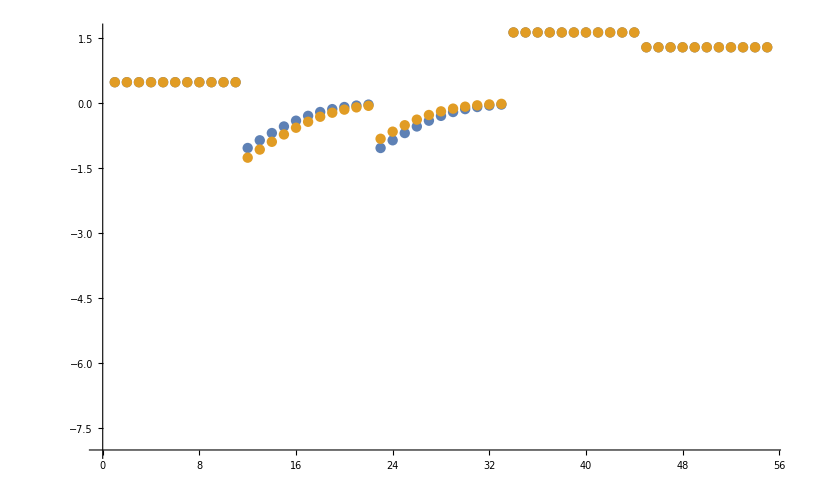

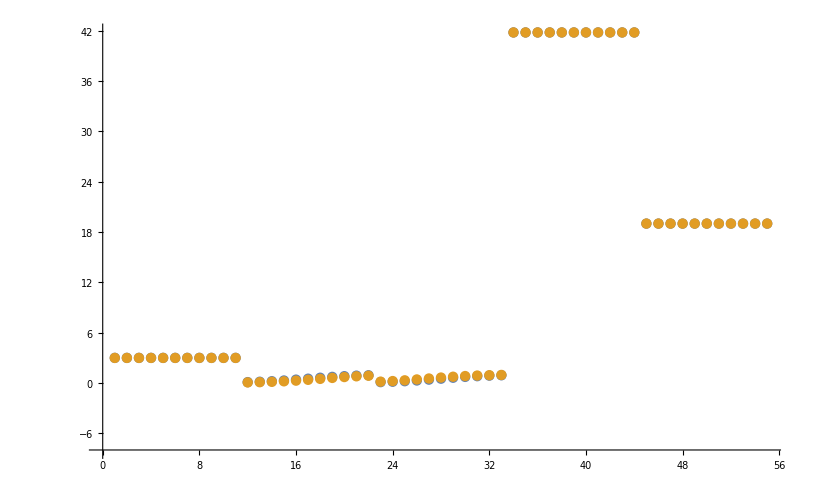

```mathematica
dataSetI=3;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

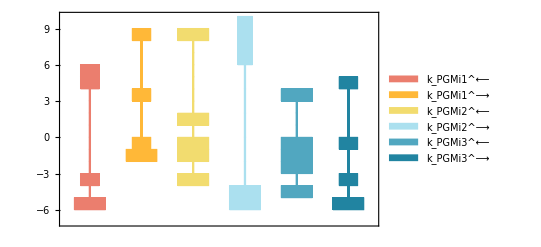

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

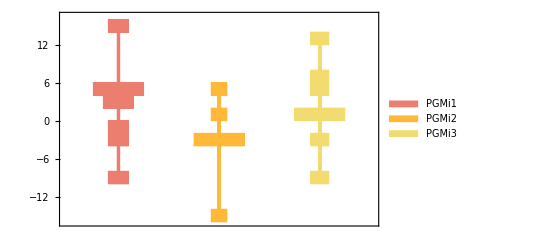

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

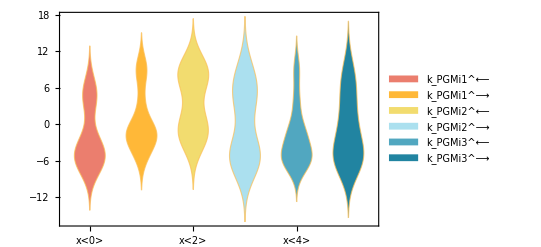

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

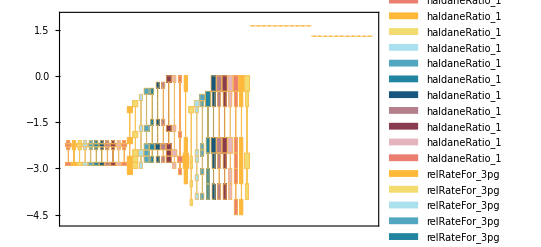

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

7.49616 | 8.37024 | 5.68272 | 1.6719 | 1.22906 | 4.78981
1.22828 | 5.6632 | 5.69368 | 5.51251 | 7.09249 | 3.26277

#### Parameter Cluster Plots (Optional)

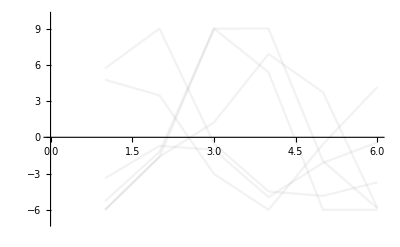

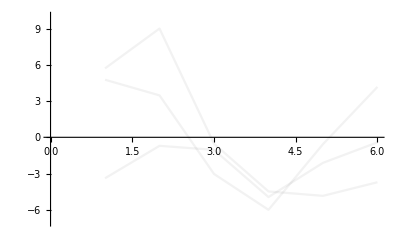
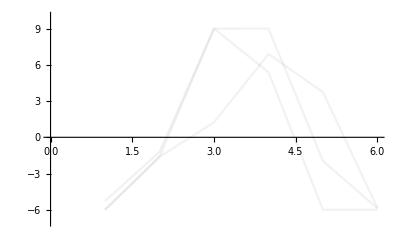

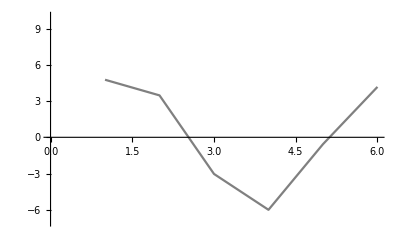
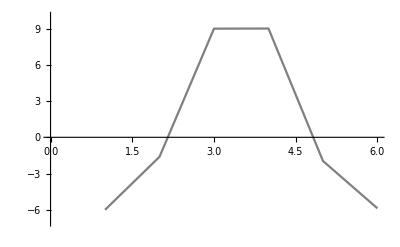

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00021 | 0.000160183 | 23.7225
0.000097 | 0.0000998907 | 2.98011

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
41.7812 | -0.0000142966 | 100.
18.9914 | -0.0000265441 | 100.

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.9815 | 2.9775 | 0.134023

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.9815 | 2.9775 | 0.134023

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

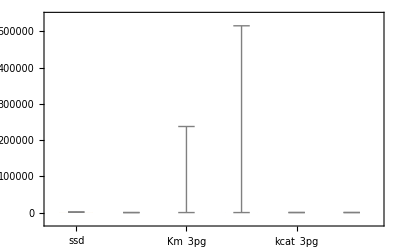

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit =10;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pgmi already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\rateconst_labels_pgmi.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\S_pgmi.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGMi[c],E_PGMi[c]&2pg,2pg[c],3pg[c],E_PGMi[c]&3pg}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\species_pgmi.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGMi1: 2pg[c] + E_PGMi[c] <=> E_PGMi[c]&2pg,PGMi2: E_PGMi[c]&3pg <=> 3pg[c] + E_PGMi[c],PGMi3: E_PGMi[c]&2pg <=> E_PGMi[c]&3pg}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\reactions_pgmi.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGMi[c],E_PGMi[c]&2pg,E_PGMi[c]&3pg}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PGMi1_rev*k_PGMi2_fwd*param_PGMi_total) - k_PGMi2_fwd*k_PGMi3_fwd*param_PGMi_total - k_PGMi1_rev*k_PGMi3_rev*param_PGMi_total)/(2pg(c)*k_PGMi1_fwd*k_PGMi2_fwd + k_PGMi1_rev*k_PGMi2_fwd + 3pg(c)*k_PGMi1_rev*k_PGMi2_rev + 2pg(c)*k_PGMi1_fwd*k_PGMi3_fwd + k_PGMi2_fwd*k_PGMi3_fwd + 3pg(c)*k_PGMi2_rev*k_PGMi3_fwd + 2pg(c)*k_PGMi1_fwd*k_PGMi3_rev + k_PGMi1_rev*k_PGMi3_rev + 3pg(c)*k_PGMi2_rev*k_PGMi3_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\rateconst_clusters_pgmi.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\rateLaw_pgmi.txt